# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
colors=Append[Table[ColorData["Rainbow"][i],{i,{0.3,0.6,0.7,0.95}}],Gray]
```

{RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.6660832, 0.7430418, 0.32293540000000004],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

## Immune escape

```mathematica
escape=Import["../escape-score/escape_scores.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding
BA.2 | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.000089996 | 0
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.000089996 | 0
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.000089996 | 0
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.000089996 | 0
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.000089996 | 0
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.000089996 | 0
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.000089996 | 0
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.000089996 | 0
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.000089996 | 0
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.000089996 | 0
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.000089996 | 0
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.000089996 | 0
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.000089996 | 0
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.000089996 | 0
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.000089996 | 0
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.000089996 | 0
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.000089996 | 0
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.000089996 | 0
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.000089996 | 0
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.000089996 | 0
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.000089996 | 0
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.000089996 | 0
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.000089996 | 0
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.000089996 | 0
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.000089996 | 0
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.000089996 | 0
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.000089996 | 0
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.000089996 | 0
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.000089996 | 0
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.000089996 | 0
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.000089996 | 0
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.000089996 | 0
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.000089996 | 0
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.000089996 | 0
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.000089996 | 0
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.000089996 | 0
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.000089996 | 0
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.000089996 | 0
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.000089996 | 0
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.000089996 | 0
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.000089996 | 0
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.000089996 | 0
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.000089996 | 0
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.000089996 | 0
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.000089996 | 0
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.000089996 | 0
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.000089996 | 0
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.000089996 | 0
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.000089996 | 0
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.000089996 | 0
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.000089996 | 0
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.000089996 | 0
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.000089996 | 0
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.000089996 | 0
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.000089996 | 0
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.000089996 | 0
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.000089996 | 0
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.000089996 | 0
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.000089996 | 0
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.000089996 | 0
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.000089996 | 0
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.000089996 | 0
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.000089996 | 0
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.000089996 | 0
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.000089996 | 0
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.000089996 | 0
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.000089996 | 0
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.000089996 | 0
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.000089996 | 0
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.000089996 | 0
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.000089996 | 0
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.000089996 | 0
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.000089996 | 0
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.000089996 | 0
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.000089996 | 0
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.000089996 | 0
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.000089996 | 0
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.000089996 | 0
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.000089996 | 0
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.000089996 | 0
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.000089996 | 0
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.000089996 | 0
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.162048 | 0.13507
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.000089996 | 0
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.000089996 | 0
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.000089996 | 0
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973
BA.4.8 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.46306
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831
BA.5.2.15 | 22B (Omicron) | BA.5.2.15 | BA.5.2.15 | 0.386325 | 0.55831
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.22218
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339
BQ.1 | 22B (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197
BQ.1.1 | 22B (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831
XAB | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAA | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAD | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAF | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XAE | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.26796
XAH | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAC | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
XAJ | 21L (Omicron) | BA.2.12 | BA.2.12 | 0.386325 | 0.35483
XAL | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAG | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | -0.28094
XAP | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XAR | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XAK | 21L (Omicron) | BA.2 | BA.2 | 0.276938 | 1.15166
XAM | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0.75567
XAT | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
XAU | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XAN | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
XAW | 21L (Omicron) | BA.2 | BA.2 | 0.212 | 0.91409
XAV | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
XAS | 21L (Omicron) | B.1.1.529 | B.1.1.529 | 0.386325 | 0.55831
XAQ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XBB | recombinant | XBB | XBB | 0.907001 | 0.40687
XAZ | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
XG | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XE | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XH | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
XK | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -3.62446
XN | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XJ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XL | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XR | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XM | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XQ | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
XT | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.17271
XV | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | -0.17271
XW | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XU | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | -0.09525
XZ | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0
XY | 21L (Omicron) | BA.2 | BA.2 | -0.000089996 | 0

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],_->colors[[5]] }
```

{21L (Omicron)→RGBColor[0.2979596, 0.5657928, 0.7522386000000001],22A (Omicron)→RGBColor[0.6660832, 0.7430418, 0.32293540000000004],22B (Omicron)→RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],22D (Omicron)→RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.28953 | 1.34365 | 1.2489
USA | BA.1 | 0.65487 | 0.699821 | 0.615384
USA | BA.1.1 | 0.680337 | 0.693929 | 0.670963
USA | BA.1.1.1 | 0.678831 | 0.696048 | 0.659866
USA | BA.1.1.10 | 0.71352 | 0.823396 | 0.603084
USA | BA.1.1.14 | 0.113713 | 0.185715 | 0.0635477
USA | BA.1.1.16 | 0.484352 | 0.631842 | 0.403094
USA | BA.1.1.18 | 0.64552 | 0.683759 | 0.609819
USA | BA.1.1.2 | 0.263297 | 0.359924 | 0.197287
USA | BA.1.15 | 0.616303 | 0.669173 | 0.559007
USA | BA.1.15.2 | 0.411325 | 0.522638 | 0.323323
USA | BA.1.17.2 | 0.38822 | 0.575421 | 0.233398
USA | BA.1.18 | 0.281002 | 0.445646 | 0.172725
USA | BA.1.20 | 0.367414 | 0.482672 | 0.25937
USA | BA.2.1 | 1.03295 | 1.06438 | 0.994342
USA | BA.2.10 | 0.897064 | 0.927035 | 0.862624
USA | BA.2.10.1 | 0.885568 | 0.98221 | 0.819162
USA | BA.2.12 | 1.17509 | 1.216 | 1.13226
USA | BA.2.12.1 | 1.1937 | 1.20061 | 1.18644
USA | BA.2.13 | 1.21318 | 1.24313 | 1.18869
USA | BA.2.13.1 | 1.31067 | 1.3377 | 1.28292
USA | BA.2.16 | 0.932991 | 1.03363 | 0.814398
USA | BA.2.18 | 1.20337 | 1.22686 | 1.17478
USA | BA.2.20 | 1.01653 | 1.07899 | 0.949838
USA | BA.2.21 | 0.984023 | 1.03102 | 0.939698
USA | BA.2.22 | 1.069 | 1.1067 | 1.02874
USA | BA.2.23 | 1.10328 | 1.1577 | 1.0705
USA | BA.2.23.1 | 0.778143 | 0.983998 | 0.619205
USA | BA.2.26 | 0.928095 | 0.965192 | 0.891354
USA | BA.2.3 | 1.00236 | 1.01156 | 0.991439
USA | BA.2.3.10 | 0.871366 | 1.0118 | 0.742445
USA | BA.2.3.14 | 0.166973 | 0.28466 | 0.105592
USA | BA.2.3.17 | 0.987858 | 1.02783 | 0.945345
USA | BA.2.3.2 | 1.00863 | 1.13021 | 0.923056
USA | BA.2.3.4 | 0.88527 | 1.03881 | 0.764286
USA | BA.2.3.6 | 0.333838 | 0.431059 | 0.276747
USA | BA.2.31 | 1.037 | 1.0939 | 1.00926
USA | BA.2.32 | 1.06682 | 1.18752 | 0.981982
USA | BA.2.36 | 1.1325 | 1.18549 | 1.07936
USA | BA.2.37 | 0.959711 | 1.07713 | 0.890118
USA | BA.2.38 | 1.25568 | 1.2938 | 1.21359
USA | BA.2.40.1 | 0.486768 | 0.549788 | 0.427768
USA | BA.2.41 | 0.948946 | 1.06164 | 0.823462
USA | BA.2.47 | 0.605314 | 0.761802 | 0.462125
USA | BA.2.48 | 1.19545 | 1.22855 | 1.16176
USA | BA.2.5 | 0.473825 | 0.718516 | 0.330657
USA | BA.2.52 | 0.399446 | 0.507248 | 0.304581
USA | BA.2.56 | 1.18497 | 1.24234 | 1.11911
USA | BA.2.59 | 0.911471 | 1.19414 | 0.702415
USA | BA.2.6 | 0.875233 | 1.00318 | 0.724428
USA | BA.2.65 | 1.09047 | 1.12071 | 1.06193
USA | BA.2.7 | 0.92296 | 0.956342 | 0.887666
USA | BA.2.72 | 0.780316 | 0.884075 | 0.697176
USA | BA.2.73 | 0.900638 | 1.01478 | 0.82193
USA | BA.2.75 | 1.50262 | 1.54177 | 1.46382
USA | BA.2.75.2 | 1.0365 | 1.20329 | 0.885543
USA | BA.2.76 | 1.21922 | 1.29534 | 1.1573
USA | BA.2.8 | 0.193035 | 0.276803 | 0.130459
USA | BA.2.9 | 1.02622 | 1.03513 | 1.01609
USA | BA.2.9.2 | 0.756817 | 0.883768 | 0.619683
USA | BA.2.9.3 | 0.369654 | 0.41934 | 0.308406
USA | BA.4 | 1.46672 | 1.48457 | 1.45225
USA | BA.4.1 | 1.45367 | 1.46244 | 1.445
USA | BA.4.1.1 | 1.40455 | 1.43789 | 1.37614
USA | BA.4.1.6 | 1.36264 | 1.40094 | 1.3305
USA | BA.4.1.8 | 1.53052 | 1.57032 | 1.48869
USA | BA.4.2 | 1.42604 | 1.45048 | 1.40718
USA | BA.4.3 | 1.42703 | 1.46613 | 1.38976
USA | BA.4.4 | 1.44132 | 1.46304 | 1.41527
USA | BA.4.6 | 1.73009 | 1.7451 | 1.71828
USA | BA.5 | 1.61237 | 1.63299 | 1.59474
USA | BA.5.1 | 1.63402 | 1.64747 | 1.62334
USA | BA.5.1.1 | 1.57812 | 1.5941 | 1.56395
USA | BA.5.1.10 | 1.62975 | 1.64904 | 1.60942
USA | BA.5.1.12 | 0.731989 | 0.88955 | 0.602126
USA | BA.5.1.18 | 1.29486 | 1.34933 | 1.22637
USA | BA.5.1.19 | 1.23489 | 1.32029 | 1.11661
USA | BA.5.1.2 | 1.46731 | 1.50818 | 1.43646
USA | BA.5.1.21 | 1.06798 | 1.27002 | 0.91846
USA | BA.5.1.3 | 1.5464 | 1.57562 | 1.5149
USA | BA.5.1.5 | 1.41304 | 1.47136 | 1.36231
USA | BA.5.1.6 | 1.54157 | 1.58333 | 1.50719
USA | BA.5.1.7 | 0.999915 | 1.16581 | 0.867884
USA | BA.5.10.1 | 0.914809 | 1.09946 | 0.763379
USA | BA.5.2 | 1.68334 | 1.69806 | 1.67229
USA | BA.5.2.1 | 1.63533 | 1.64626 | 1.62502
USA | BA.5.2.16 | 1.25921 | 1.33131 | 1.19232
USA | BA.5.2.19 | 1.29545 | 1.37312 | 1.2197
USA | BA.5.2.2 | 1.22754 | 1.29621 | 1.15554
USA | BA.5.2.20 | 1.62811 | 1.65581 | 1.6033
USA | BA.5.2.21 | 1.57303 | 1.59365 | 1.54884
USA | BA.5.2.22 | 1.46411 | 1.50444 | 1.42418
USA | BA.5.2.3 | 1.42169 | 1.47004 | 1.38415
USA | BA.5.2.6 | 1.06831 | 1.1646 | 0.972559
USA | BA.5.2.8 | 0.853555 | 0.968838 | 0.75049
USA | BA.5.2.9 | 1.68392 | 1.70135 | 1.66894
USA | BA.5.3 | 1.37003 | 1.41046 | 1.32633
USA | BA.5.3.1 | 1.54584 | 1.57798 | 1.51924
USA | BA.5.5 | 1.501 | 1.51449 | 1.49083
USA | BA.5.5.1 | 1.44841 | 1.47654 | 1.41077
USA | BA.5.5.2 | 1.33654 | 1.38641 | 1.2872
USA | BA.5.5.3 | 0.967673 | 1.02747 | 0.882643
USA | BA.5.6 | 1.58397 | 1.59801 | 1.57074
USA | BA.5.6.1 | 1.18283 | 1.26549 | 1.10949
USA | BA.5.6.2 | 1.24583 | 1.32285 | 1.18345
USA | BA.5.8 | 1.48082 | 1.51624 | 1.45332
USA | BA.5.9 | 0.857859 | 1.08834 | 0.708994
USA | BE.1 | 1.60518 | 1.62632 | 1.59188
USA | BE.1.1 | 1.55567 | 1.57749 | 1.53493
USA | BE.1.1.1 | 1.12231 | 1.28545 | 0.952867
USA | BE.1.2 | 1.09907 | 1.28644 | 0.948557
USA | BE.2 | 1.44147 | 1.47133 | 1.40522
USA | BE.3 | 1.56259 | 1.57909 | 1.54683
USA | BF.1 | 1.42571 | 1.45992 | 1.39345
USA | BF.1.1 | 0.703766 | 0.767381 | 0.648263
USA | BF.10 | 1.66226 | 1.67475 | 1.64798
USA | BF.11 | 1.32245 | 1.38422 | 1.24677
USA | BF.13 | 1.44806 | 1.48979 | 1.40343
USA | BF.16 | 0.936157 | 1.03108 | 0.839108
USA | BF.21 | 1.58312 | 1.60414 | 1.55962
USA | BF.25 | 0.411575 | 0.536459 | 0.32883
USA | BF.3 | 0.808959 | 0.996296 | 0.647638
USA | BF.4 | 1.4006 | 1.43653 | 1.35965
USA | BF.5 | 1.66579 | 1.68512 | 1.64072
USA | BF.7 | 1.60293 | 1.63892 | 1.56892
USA | BF.8 | 1.51982 | 1.54028 | 1.49379
USA | BF.9 | 1.48411 | 1.51231 | 1.44711
USA | BG.2 | 1.22387 | 1.23959 | 1.20931
USA | BG.4 | 0.759933 | 0.922242 | 0.579455
USA | BG.5 | 1.28955 | 1.32795 | 1.26295
USA | BK.1 | 1.50458 | 1.54279 | 1.46818
USA | XAP | 0.332588 | 0.419882 | 0.254431
USA | XAS | 0.796927 | 0.934393 | 0.697328
USA | XE | 0.214175 | 0.258984 | 0.170242
USA | XZ | 0.995909 | 1.14048 | 0.890295
USA | other | 0.00341806 | 0.00345777 | 0.00337597

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.2,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.19,BA.5.1.2,BA.5.1.21,BA.5.1.3,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.3,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.1,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.2,BE.3,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.16,BF.21,BF.3,BF.4,BF.5,BF.7,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,XAP,XAS,XE,XZ}

```mathematica
Length[pangoLineages]
```

120

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.580784

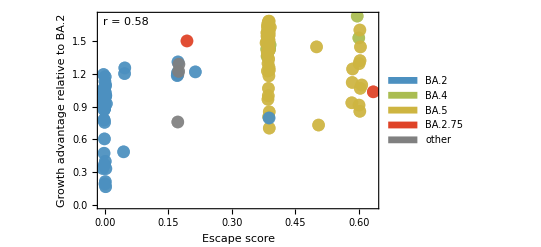

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.644274

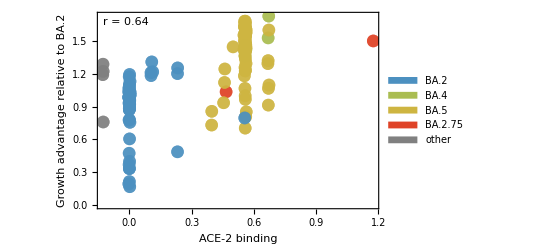

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.005]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.005]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.871479

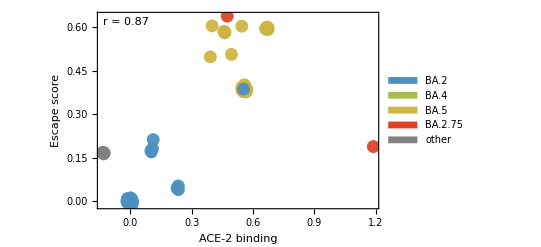

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_escape_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1 and binding X_2

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{x1,x2},{x1,x2}]
```

FittedModel[0.886605+0.136873 x1+0.725781 x2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.886605 | 0.0407479 | 21.7583 | 6.1625×10^-43
x1 | 0.136873 | 0.245592 | 0.557317 | 0.578375
x2 | 0.725781 | 0.182435 | 3.97829 | 0.00012072